# Computing the Transfer function for LISA equal armlength case

"Jonathan Gair and Martina Muratore26-05-23"

## Computing the Upsilon from ‘’ Pieroni et all ‘’

## defining the spacecraft position

#### Spacecraft position in terms of mode of the LISA triangles

```mathematica
subs={Subscript[δ,5]->-0.004859508251784215,Subscript[δ,6]->0.009363952212402271,T=SetPrecision[2.5*10^9/299792458//N,50]};
```

```mathematica
x1=SetPrecision[{-(Subscript[δ,5]/Sqrt[3]),-(1/Sqrt[3])+Subscript[δ,6]/Sqrt[3],0}*T(*/.subs//N*),50]
x2=SetPrecision[{1/2+Subscript[δ,5]/(2 Sqrt[3])+Subscript[δ,6]/2,1/(2 Sqrt[3])+Subscript[δ,5]/2-Subscript[δ,6]/(2 Sqrt[3]),0}*T/.subs//N,50];
x3=SetPrecision[{-(1/2)+Subscript[δ,5]/(2 Sqrt[3])-Subscript[δ,6]/2,1/(2 Sqrt[3])-Subscript[δ,5]/2-Subscript[δ,6]/(2 Sqrt[3]),0}*T/.subs//N,50];
```

{-0.5773502691896257645091487805019574556476017512701 T δ_5,T (-0.5773502691896257645091487805019574556476017512701+0.57735026918962576450914878050195745564760175127013 δ_6),0}

#### Considering equal arm-lengths

```mathematica
subs={Subscript[δ,5]->0,Subscript[δ,6]->0};
T=SetPrecision[2.5*10^9/299792458,50]
T = SetPrecision[8.30,50]
```

8.339102379953800436851452104747295379638671875

8.300000000000000710542735760100185871124267578125

```mathematica
x1=SetPrecision[{-(Subscript[δ,5]/Sqrt[3]),-(1/Sqrt[3])+Subscript[δ,6]/Sqrt[3],0}*T/.subs//N,50]
x2=SetPrecision[{1/2+Subscript[δ,5]/(2 Sqrt[3])+Subscript[δ,6]/2,1/(2 Sqrt[3])+Subscript[δ,5]/2-Subscript[δ,6]/(2 Sqrt[3]),0}*T/.subs//N,50]
x3=SetPrecision[{-(1/2)+Subscript[δ,5]/(2 Sqrt[3])-Subscript[δ,6]/2,1/(2 Sqrt[3])-Subscript[δ,5]/2-Subscript[δ,6]/(2 Sqrt[3]),0}*T/.subs//N,50]
```

{0,-4.7920072342738944115581034566275775432586669921875,0}

{4.1500000000000003552713678800500929355621337890625,2.3960036171369472057790517283137887716293334960938,0}

{-4.1500000000000003552713678800500929355621337890625,2.3960036171369472057790517283137887716293334960938,0}

#### defining the norm of the lengths of the spacecraft arm-lengths

```mathematica
L21=Simplify[SetPrecision[Norm[x1-x2]/.subs//N,50],T>0]
L31=Simplify[SetPrecision[Norm[x1-x3]/.subs//N,50],T>0]
L32=Simplify[SetPrecision[Norm[x3-x2]/.subs//N,50],T>0]

L12=L21;
L13=L31;
L23=L32;
f12=f21;
f13=f31;
f23=f32;


f21=1/(2*π*L12);
f31=1/(2*π*L13);
f32=1/(2*π*L23);
```

8.300000000000000710542735760100185871124267578125

8.300000000000000710542735760100185871124267578125

8.300000000000000710542735760100185871124267578125

#### defining the versor of the spacecraft arm-lengths

```mathematica
lhat12=Simplify[(x2-x1)/Norm[x2-x1]/.subs,T>0]
lhat13=Simplify[(x3-x1)/Norm[x3-x1]/.subs,T>0]
lhat23=Simplify[(x3-x2)/Norm[x3-x2]/.subs,T>0]
lhat21=-lhat12;
lhat31=-lhat13;
lhat32=-lhat23;
```

{0.4999999999999999877999874691139979539733211128909,0.8660254037844386538074036895767768616925885097022,0}

{-0.4999999999999999877999874691139979539733211128909,0.8660254037844386538074036895767768616925885097022,0}

{-1.,0.,0}

## defining the GW vector and polarization tensor

```mathematica
hatk[th_,ph_]:={Sin[th]*Cos[ph],Sin[th]*Sin[ph],Cos[th]};
hatu[th_,ph_]:={Sin[ph],-Cos[ph],0};
hatv[th_,ph_]:={Cos[th]*Cos[ph],Cos[th]*Sin[ph],-Sin[th]};
eplus[th_,ph_]:=Simplify[Outer[Times,hatu[th,ph],hatu[th,ph]]-Outer[Times,hatv[th,ph],hatv[th,ph]]];
ecross[th_,ph_]:=Simplify[Outer[Times,hatu[th,ph],hatv[th,ph]]+Outer[Times,hatv[th,ph],hatu[th,ph]]];
```

## computing the Upsilon

#### computing the ξij

```mathematica
xi12plus[f_,th_,ph_]:=Exp[-π*I*f*L12*(hatk[th,ph].lhat12-1)]*Sinc[π*f*L12*(1+hatk[th,ph].lhat12)]*0.5*(lhat12.eplus[th,ph].lhat12);
xi12cross[f_,th_,ph_]:=Exp[-π*I*f*L12*(hatk[th,ph].lhat12-1)]*Sinc[π*f*L12*(1+hatk[th,ph].lhat12)]*0.5*(lhat12.ecross[th,ph].lhat12);
xi21plus[f_,th_,ph_]:=Exp[-π*I*f*L21*(hatk[th,ph].lhat21-1)]*Sinc[π*f*L21*(1+hatk[th,ph].lhat21)]*0.5*(lhat21.eplus[th,ph].lhat21);
xi21cross[f_,th_,ph_]:=Exp[-π*I*f*L21*(hatk[th,ph].lhat21-1)]*Sinc[π*f*L21*(1+hatk[th,ph].lhat21)]*0.5*(lhat21.ecross[th,ph].lhat21);
xi13plus[f_,th_,ph_]:=Exp[-π*I*f*L13*(hatk[th,ph].lhat13-1)]*Sinc[π*f*L13*(1+hatk[th,ph].lhat13)]*0.5*(lhat13.eplus[th,ph].lhat13);
xi13cross[f_,th_,ph_]:=Exp[-π*I*f*L13*(hatk[th,ph].lhat13-1)]*Sinc[π*f*L13*(1+hatk[th,ph].lhat13)]*0.5*(lhat13.ecross[th,ph].lhat13);
xi31plus[f_,th_,ph_]:=Exp[-π*I*f*L31*(hatk[th,ph].lhat31-1)]*Sinc[π*f*L31*(1+hatk[th,ph].lhat31)]*0.5*(lhat31.eplus[th,ph].lhat31);
xi31cross[f_,th_,ph_]:=Exp[-π*I*f*L31*(hatk[th,ph].lhat31-1)]*Sinc[π*f*L31*(1+hatk[th,ph].lhat31)]*0.5*(lhat31.ecross[th,ph].lhat31);
xi23plus[f_,th_,ph_]:=Exp[-π*I*f*L23*(hatk[th,ph].lhat23-1)]*Sinc[π*f*L23*(1+hatk[th,ph].lhat23)]*0.5*(lhat23.eplus[th,ph].lhat23);
xi23cross[f_,th_,ph_]:=Exp[-π*I*f*L23*(hatk[th,ph].lhat23-1)]*Sinc[π*f*L23*(1+hatk[th,ph].lhat23)]*0.5*(lhat23.ecross[th,ph].lhat23);
xi32plus[f_,th_,ph_]:=Exp[-π*I*f*L32*(hatk[th,ph].lhat32-1)]*Sinc[π*f*L32*(1+hatk[th,ph].lhat32)]*0.5*(lhat32.eplus[th,ph].lhat32);
xi32cross[f_,th_,ph_]:=Exp[-π*I*f*L32*(hatk[th,ph].lhat32-1)]*Sinc[π*f*L32*(1+hatk[th,ph].lhat32)]*0.5*(lhat32.ecross[th,ph].lhat32);
```

#### computing the upsilon

```mathematica
Upsilon1212plusArg[f_,th_,ph_]:=xi12plus[f,th,ph]*Conjugate[xi12plus[f,th,ph]];
Upsilon1213plusArg[f_,th_,ph_]:=xi12plus[f,th,ph]*Conjugate[xi13plus[f,th,ph]];
Upsilon1223plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x2)]*xi12plus[f,th,ph]*Conjugate[xi23plus[f,th,ph]];
Upsilon1221plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x2)]*xi12plus[f,th,ph]*Conjugate[xi21plus[f,th,ph]];
Upsilon1231plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x3)]*xi12plus[f,th,ph]*Conjugate[xi31plus[f,th,ph]];
Upsilon1232plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x3)]*xi12plus[f,th,ph]*Conjugate[xi32plus[f,th,ph]];
Upsilon1313plusArg[f_,th_,ph_]:=xi13plus[f,th,ph]*Conjugate[xi13plus[f,th,ph]];
Upsilon1323plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x2)]*xi13plus[f,th,ph]*Conjugate[xi23plus[f,th,ph]];
Upsilon1321plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x2)]*xi13plus[f,th,ph]*Conjugate[xi21plus[f,th,ph]];
Upsilon1331plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x3)]*xi13plus[f,th,ph]*Conjugate[xi31plus[f,th,ph]];
Upsilon1332plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x3)]*xi13plus[f,th,ph]*Conjugate[xi32plus[f,th,ph]];
Upsilon2323plusArg[f_,th_,ph_]:=xi23plus[f,th,ph]*Conjugate[xi23plus[f,th,ph]];
Upsilon2321plusArg[f_,th_,ph_]:=xi23plus[f,th,ph]*Conjugate[xi21plus[f,th,ph]];
Upsilon2331plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x2-x3)]*xi23plus[f,th,ph]*Conjugate[xi31plus[f,th,ph]];
Upsilon2332plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x2-x3)]*xi23plus[f,th,ph]*Conjugate[xi32plus[f,th,ph]];
Upsilon2121plusArg[f_,th_,ph_]:=xi21plus[f,th,ph]*Conjugate[xi21plus[f,th,ph]];
Upsilon2131plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x2-x3)]*xi21plus[f,th,ph]*Conjugate[xi31plus[f,th,ph]];
Upsilon2132plusArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x2-x3)]*xi21plus[f,th,ph]*Conjugate[xi32plus[f,th,ph]];
Upsilon3131plusArg[f_,th_,ph_]:=xi31plus[f,th,ph]*Conjugate[xi31plus[f,th,ph]];
Upsilon3132plusArg[f_,th_,ph_]:=xi31plus[f,th,ph]*Conjugate[xi32plus[f,th,ph]];
Upsilon3232plusArg[f_,th_,ph_]:=xi32plus[f,th,ph]*Conjugate[xi32plus[f,th,ph]];
Upsilon1212crossArg[f_,th_,ph_]:=xi12cross[f,th,ph]*Conjugate[xi12cross[f,th,ph]];
Upsilon1213crossArg[f_,th_,ph_]:=xi12cross[f,th,ph]*Conjugate[xi13cross[f,th,ph]];
Upsilon1223crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x2)]*xi12cross[f,th,ph]*Conjugate[xi23cross[f,th,ph]];
Upsilon1221crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x2)]*xi12cross[f,th,ph]*Conjugate[xi21cross[f,th,ph]];
Upsilon1231crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x3)]*xi12cross[f,th,ph]*Conjugate[xi31cross[f,th,ph]];
Upsilon1232crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x3)]*xi12cross[f,th,ph]*Conjugate[xi32cross[f,th,ph]];
Upsilon1313crossArg[f_,th_,ph_]:=xi13cross[f,th,ph]*Conjugate[xi13cross[f,th,ph]];
Upsilon1323crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x2)]*xi13cross[f,th,ph]*Conjugate[xi23cross[f,th,ph]];
Upsilon1321crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x2)]*xi13cross[f,th,ph]*Conjugate[xi21cross[f,th,ph]];
Upsilon1331crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x3)]*xi13cross[f,th,ph]*Conjugate[xi31cross[f,th,ph]];
Upsilon1332crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x1-x3)]*xi13cross[f,th,ph]*Conjugate[xi32cross[f,th,ph]];
Upsilon2323crossArg[f_,th_,ph_]:=xi23cross[f,th,ph]*Conjugate[xi23cross[f,th,ph]];
Upsilon2321crossArg[f_,th_,ph_]:=xi23cross[f,th,ph]*Conjugate[xi21cross[f,th,ph]];
Upsilon2331crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x2-x3)]*xi23cross[f,th,ph]*Conjugate[xi31cross[f,th,ph]];
Upsilon2332crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x2-x3)]*xi23cross[f,th,ph]*Conjugate[xi32cross[f,th,ph]];
Upsilon2121crossArg[f_,th_,ph_]:=xi21cross[f,th,ph]*Conjugate[xi21cross[f,th,ph]];
Upsilon2131crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x2-x3)]*xi21cross[f,th,ph]*Conjugate[xi31cross[f,th,ph]];
Upsilon2132crossArg[f_,th_,ph_]:=Exp[-2*π*I*f*hatk[th,ph].(x2-x3)]*xi21cross[f,th,ph]*Conjugate[xi32cross[f,th,ph]];
Upsilon3131crossArg[f_,th_,ph_]:=xi31cross[f,th,ph]*Conjugate[xi31cross[f,th,ph]];
Upsilon3132crossArg[f_,th_,ph_]:=xi31cross[f,th,ph]*Conjugate[xi32cross[f,th,ph]];
Upsilon3232crossArg[f_,th_,ph_]:=xi32cross[f,th,ph]*Conjugate[xi32cross[f,th,ph]];
```

#### creating a list with all the upsilon

```mathematica
UpsList[f_,th_,ph_]:={Upsilon1212plusArg[f,th,ph]/.subs,Upsilon1213plusArg[f,th,ph]/.subs,Upsilon1223plusArg[f,th,ph]/.subs,Upsilon1221plusArg[f,th,ph]/.subs,Upsilon1231plusArg[f,th,ph]/.subs,Upsilon1232plusArg[f,th,ph]/.subs,Upsilon1313plusArg[f,th,ph]/.subs,Upsilon1323plusArg[f,th,ph]/.subs,Upsilon1321plusArg[f,th,ph]/.subs,Upsilon1331plusArg[f,th,ph]/.subs,Upsilon1332plusArg[f,th,ph]/.subs,Upsilon2323plusArg[f,th,ph]/.subs,Upsilon2321plusArg[f,th,ph]/.subs,Upsilon2331plusArg[f,th,ph]/.subs,Upsilon2332plusArg[f,th,ph]/.subs,Upsilon2121plusArg[f,th,ph]/.subs,Upsilon2131plusArg[f,th,ph]/.subs,Upsilon2132plusArg[f,th,ph]/.subs,Upsilon3131plusArg[f,th,ph]/.subs,Upsilon3132plusArg[f,th,ph]/.subs,Upsilon3232plusArg[f,th,ph]/.subs,Upsilon1212crossArg[f,th,ph]/.subs,Upsilon1213crossArg[f,th,ph]/.subs,Upsilon1223crossArg[f,th,ph]/.subs,Upsilon1221crossArg[f,th,ph]/.subs,Upsilon1231crossArg[f,th,ph]/.subs,Upsilon1232crossArg[f,th,ph]/.subs,Upsilon1313crossArg[f,th,ph]/.subs,Upsilon1323crossArg[f,th,ph]/.subs,Upsilon1321crossArg[f,th,ph]/.subs,Upsilon1331crossArg[f,th,ph]/.subs,Upsilon1332crossArg[f,th,ph]/.subs,Upsilon2323crossArg[f,th,ph]/.subs,Upsilon2321crossArg[f,th,ph]/.subs,Upsilon2331crossArg[f,th,ph]/.subs,Upsilon2332crossArg[f,th,ph]/.subs,Upsilon2121crossArg[f,th,ph]/.subs,Upsilon2131crossArg[f,th,ph]/.subs,Upsilon2132crossArg[f,th,ph]/.subs,Upsilon3131crossArg[f,th,ph]/.subs,Upsilon3132crossArg[f,th,ph]/.subs,Upsilon3232crossArg[f,th,ph]/.subs};
```

## Evaluating the upsilon for LISA frequency band

#### defining the frequency range

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
Nfs =800;
freqs=SetPrecision[logspace[Log10[5*10^-6],Log10[1*10^-1],Nfs],100];
```

#### evaluating the upsilon for the uniform direction

```mathematica
getangles[vec_]:=Module[{theta, phi, phir},
theta = ArcCos[vec[[3]]];
phi = ArcTan[vec[[1]]/Sin[theta], vec[[2]]/Sin[theta]];
If[phi < 0, phir = phi + 2 Pi, phir = phi];
Return[{theta,phir}];
]
```

```mathematica
unisphere = SpherePoints[1000];
```

```mathematica
getanglesθ[vec_]:=Module[{theta},
theta = ArcCos[vec[[3]]];
Return[theta];
]
```

```mathematica
getanglesϕ[vec_]:=Module[{theta, phi, phir},
theta = ArcCos[vec[[3]]];
phi = ArcTan[vec[[1]]/Sin[theta], vec[[2]]/Sin[theta]];
If[phi < 0, phir = phi + 2 Pi, phir = phi];
Return[phir];
]
```

```mathematica
thetas=Map[getanglesθ,unisphere];
```

```mathematica
phis=Map[getanglesϕ,unisphere];
```

```mathematica
(*ransphere = ParallelMap[hatk[thetas[[#]], phis[[#]]]&, Range[1000]];*)
```

```mathematica
(*Graphics3D[Point[ransphere]]*)
```

-Graphics3D-

```mathematica
(*veck = ParallelMap[hatk[thetas[[#]], phis[[#]]]&, Range[1000]];*)
```

#### evaluating the upsilon for the uniform direction

```mathematica
Nsph = 1000;
(*thetas=SetPrecision[ArcCos[-1.+2.*RandomReal[{0,1},Nfs*Nsph]],50];
phis=SetPrecision[2*π*RandomReal[{0,1},Nfs*Nsph],50];*)
```

```mathematica
(*ResultNsph1000=SetPrecision[ParallelTable[Sum[UpsList[freqs[[i]],thetas[[(i-1)*Nsph+j]],phis[[(i-1)*Nsph+j]]],{j,1,Nsph}]/Nsph,{i,1,Nfs}],50];*)
```

```mathematica
ResultNsph1000=SetPrecision[ParallelTable[Sum[UpsList[freqs[[i]],thetas[[j]],phis[[j]]],{j,1,Nsph}]/Nsph,{i,1,Nfs}],50];
```

## Defining the S^GW matrix

We are using Conjugate[S_(ij,mn)] = S_(mn,ij)

(Y1212 | Y1213 | Y1223 | Y1221 | Y1231 | Y1232
Conj[Y1213] | Y1313 | Y1323 | Y1321 | Y1331 | Y1332
Conj[Y1223] | Conj[Y1323] | Y2323 | Y2321 | Y2331 | Y2332
Conj[Y1221] | Conj[Y
1321] | Conj[Y2321] | Y2121 | Y2131 | Y2132
Conj[Y1231] | Conj[Y1331] | Conj[Y2331] | Conj[Y2131] | Y3131 | Y3132
Conj[Y1232] | Conj[Y1332] | Conj[Y2332] | Conj[Y2132] | Conj[Y3132] | Y3232)

```mathematica
(** Ordering of indices: {12, 13, 23, 21, 31, 32} **)
Smatrix1000=SetPrecision[ParallelTable[{{(ResultNsph1000[[i]][[1]]+ResultNsph1000[[i]][[22]])*freqs[[i]]*freqs[[i]]/(f12*f12),(ResultNsph1000[[i]][[2]]+ResultNsph1000[[i]][[23]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*I*freqs[[i]]*(L12-L13)]/(f12*f13),(ResultNsph1000[[i]][[3]]+ResultNsph1000[[i]][[24]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L12-L23)]/(f12*f23),(ResultNsph1000[[i]][[4]]+ResultNsph1000[[i]][[25]])*freqs[[i]]*freqs[[i]]/(f12*f21),(ResultNsph1000[[i]][[5]]+ResultNsph1000[[i]][[26]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L12-L31)]/(f12*f31),(ResultNsph1000[[i]][[6]]+ResultNsph1000[[i]][[27]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L12-L32)]/(f12*f32)},{Conjugate[(ResultNsph1000[[i]][[2]]+ResultNsph1000[[i]][[23]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L13-L12)]/(f13*f12),(ResultNsph1000[[i]][[7]]+ResultNsph1000[[i]][[28]])*freqs[[i]]*freqs[[i]]/(f13*f13),(ResultNsph1000[[i]][[8]]+ResultNsph1000[[i]][[29]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L13-L23)]/(f13*f23),(ResultNsph1000[[i]][[9]]+ResultNsph1000[[i]][[30]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L13-L21)]/(f13*f21),(ResultNsph1000[[i]][[10]]+ResultNsph1000[[i]][[31]])*freqs[[i]]*freqs[[i]]/(f13*f31),(ResultNsph1000[[i]][[11]]+ResultNsph1000[[i]][[32]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L13-L32)]/(f13*f32)},{Conjugate[(ResultNsph1000[[i]][[3]]+ResultNsph1000[[i]][[24]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L23-L12)]/(f23*f12),Conjugate[(ResultNsph1000[[i]][[8]]+ResultNsph1000[[i]][[29]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L23-L13)]/(f23*f13),(ResultNsph1000[[i]][[12]]+ResultNsph1000[[i]][[33]])*freqs[[i]]*freqs[[i]]/(f23*f23),(ResultNsph1000[[i]][[13]]+ResultNsph1000[[i]][[34]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L23-L21)]/(f23*f21),(ResultNsph1000[[i]][[14]]+ResultNsph1000[[i]][[35]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L23-L31)]/(f23*f31),(ResultNsph1000[[i]][[15]]+ResultNsph1000[[i]][[36]])*freqs[[i]]*freqs[[i]]/(f23*f32)},{Conjugate[(ResultNsph1000[[i]][[4]]+ResultNsph1000[[i]][[25]])]*freqs[[i]]*freqs[[i]]/(f21*f12),Conjugate[(ResultNsph1000[[i]][[9]]+ResultNsph1000[[i]][[30]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L21-L13)]/(f21*f13),Conjugate[(ResultNsph1000[[i]][[13]]+ResultNsph1000[[i]][[34]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L21-L23)]/(f21*f23),(ResultNsph1000[[i]][[16]]+ResultNsph1000[[i]][[37]])*freqs[[i]]*freqs[[i]]/(f21*f21),(ResultNsph1000[[i]][[17]]+ResultNsph1000[[i]][[38]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L21-L31)]/(f21*f31),(ResultNsph1000[[i]][[18]]+ResultNsph1000[[i]][[39]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L21-L32)]/(f21*f32)},
{Conjugate[(ResultNsph1000[[i]][[5]]+ResultNsph1000[[i]][[26]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L31-L12)]/(f31*f12),Conjugate[(ResultNsph1000[[i]][[10]]+ResultNsph1000[[i]][[31]])]*freqs[[i]]*freqs[[i]]/(f31*f13),Conjugate[(ResultNsph1000[[i]][[14]]+ResultNsph1000[[i]][[35]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L31-L23)]/(f31*f23),Conjugate[(ResultNsph1000[[i]][[17]]+ResultNsph1000[[i]][[38]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L31-L21)]/(f31*f21),(ResultNsph1000[[i]][[19]]+ResultNsph1000[[i]][[40]])*freqs[[i]]*freqs[[i]]/(f31*f31),(ResultNsph1000[[i]][[20]]+ResultNsph1000[[i]][[41]])*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L31-L32)]/(f31*f32)},{Conjugate[(ResultNsph1000[[i]][[6]]+ResultNsph1000[[i]][[27]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L32-L12)]/(f32*f12),Conjugate[(ResultNsph1000[[i]][[11]]+ResultNsph1000[[i]][[32]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L32-L13)]/(f32*f13),Conjugate[(ResultNsph1000[[i]][[15]]+ResultNsph1000[[i]][[36]])]*freqs[[i]]*freqs[[i]]/(f32*f23),Conjugate[(ResultNsph1000[[i]][[18]]+ResultNsph1000[[i]][[39]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L32-L21)]/(f32*f21),Conjugate[(ResultNsph1000[[i]][[20]]+ResultNsph1000[[i]][[41]])]*freqs[[i]]*freqs[[i]]*Exp[-2*π*ⅈ*freqs[[i]]*(L32-L31)]/(f32*f31),(ResultNsph1000[[i]][[21]]+ResultNsph1000[[i]][[42]])*freqs[[i]]*freqs[[i]]/(f32*f32)}},{i,1,Nfs}],50];
```

## Computing the TDI coefficient for the A , E ζ channels equal arm-length

### TDI variables in time first generation

```mathematica
Xol1=-((1 -d[1,3]d[3,1])(η[1,2]+d[1,2]η[2,1])+(d[1,2]d[2,1]-1)(η[1,3]+d[1,3]η[3,1]));
```

```mathematica
Yol1=-((1 -d[2,1]d[1,2])(η[2,3]+d[2,3]η[3,2])+(d[2,3]d[3,2]-1)(η[2,1]+d[2,1]η[1,2]));
```

```mathematica
Zol1=-((1 -d[3,2]d[2,3])(η[3,1]+d[3,1]η[1,3])+(d[3,1]d[1,3]-1)(η[3,2]+d[3,2]η[2,3]));
```

```mathematica
ζol1 = d[1,2](η[3,1]-η[3,2])+ d[2,3](η[1,2]-η[1,3])+ d[3,1](η[2,3]-η[2,1]);
```

### TDI variables in time second generation X,Y,Z

```mathematica
Xol2=η[3,1]*(-(d[1,2]*d[2,1]*d[1,3])-(d[1,2]*d[2,1]*d[1,3]*d[3,1]*d[1,3]) + d[1,3] + (d[1,3]*d[3,1]*d[1,2]*d[2,1]*d[1,2]d[2,1]*d[1,3]))+
η[1,3]*(-(d[1,2]*d[2,1])-(d[1,2]*d[2,1]*d[1,3]*d[3,1]) +1+ (d[1,3]*d[3,1]*d[1,2]*d[2,1]*d[1,2]d[2,1]))+η[2,1]*(-(d[1,2])-(d[1,2]*d[2,1]*d[1,3]*d[3,1]*d[1,3]*d[3,1]*d[1,2]) + (d[1,3]*d[3,1]*d[1,2] )+ (d[1,3]*d[3,1]*d[1,2]*d[2,1]*d[1,2]))+η[1,2]*(-1-(d[1,2]*d[2,1]*d[1,3]*d[3,1]*d[1,3]*d[3,1]) + (d[1,3]*d[3,1] )+ (d[1,3]*d[3,1]*d[1,2]*d[2,1]));
```

```mathematica
Yol2 = (-1+d[2,1] d[1,2]+d[2,3] d[2,1] d[3,2] d[1,2]-d[2,3] d[2,1]^2 d[3,2] d[1,2]^2) η[2,3]+(1-d[2,3] d[3,2]-d[2,3] d[2,1] d[3,2] d[1,2]+d[2,3]^2 d[2,1] d[3,2]^2 d[1,2]) η[2,1]+(-d[2,3]+d[2,3] d[2,1] d[1,2]+d[2,3]^2 d[2,1] d[3,2] d[1,2]-d[2,3]^2 d[2,1]^2 d[3,2] d[1,2]^2) η[3,2]+(d[2,1]-d[2,3] d[2,1] d[3,2]-d[2,3] d[2,1]^2 d[3,2] d[1,2]+d[2,3]^2 d[2,1]^2 d[3,2]^2 d[1,2]) η[1,2];
```

```mathematica
Zol2= (-1+d[3,2] d[2,3]+d[3,1] d[3,2] d[1,3] d[2,3]-d[3,1] d[3,2]^2 d[1,3] d[2,3]^2) η[3,1]+(1-d[3,1] d[1,3]-d[3,1] d[3,2] d[1,3] d[2,3]+d[3,1]^2 d[3,2] d[1,3]^2 d[2,3]) η[3,2]+(-d[3,1]+d[3,1] d[3,2] d[2,3]+d[3,1]^2 d[3,2] d[1,3] d[2,3]-d[3,1]^2 d[3,2]^2 d[1,3] d[2,3]^2) η[1,3]+(d[3,2]-d[3,1] d[3,2] d[1,3]-d[3,1] d[3,2]^2 d[1,3] d[2,3]+d[3,1]^2 d[3,2]^2 d[1,3]^2 d[2,3]) η[2,3];
```

### TDI variables in frequency

```mathematica
freqd = {d[1,2]->Exp[-I ω L12],d[1,3]->Exp[-I ω L13],d[3,2]->Exp[-I ω L32],d[2,1]->Exp[-I ω L12],d[3,1]->Exp[-I ω L31],d[2,3]->Exp[-I ω L32]}
```

{d[1,2]→ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω),d[1,3]→ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω),d[3,2]→ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω),d[2,1]→ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω),d[3,1]→ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω),d[2,3]→ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)}

```mathematica
Aolf = (Zol2 -Xol2)/√2//.freqd
```

1/(√2)(-((-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[1,2])-(1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[1,3]+(-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[1,3]-(-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[2,1]+(ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[2,3]+(-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[3,1]-(ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[3,1]+(1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[3,2])

```mathematica
Eolf =  (Xol2-2Yol2+Zol2)/√6//.freqd
```

1/(√6)((-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[1,2]+(1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[1,3]+(-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[1,3]+(-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[2,1]+(ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[2,3]+(-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[3,1]+(ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[3,1]+(1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[3,2]-2 ((ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[1,2]+(1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[2,1]+(-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[2,3]+(-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[3,2]))

```mathematica
Tolf = (Xol2 +Yol2+Zol2)/√3//.freqd
```

1/(√3)((-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[1,2]+(ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[1,2]+(1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[1,3]+(-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[1,3]+(1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[2,1]+(-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[2,1]+(-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[2,3]+(ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[2,3]+(-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[3,1]+(ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[3,1]+(1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)) η[3,2]+(-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)) η[3,2])

```mathematica
X2f =Xol2//.freqd;
```

```mathematica
Y2f =Yol2//.freqd;
```

```mathematica
Z2f =Zol2//.freqd;
```

### coefficient calculation

```mathematica
(** Ordering of indices: {12, 13, 23, 21, 31, 32} **)
```

```mathematica
CoeffMatrix[comb_]:={Coefficient[comb, η[1,2]],Coefficient[comb, η[1,3]],Coefficient[comb, η[2,3]],Coefficient[comb, η[2,1]],Coefficient[comb, η[3,1]],Coefficient[comb, η[3,2]]}
```

#### coefficient calculation ζ 12 13 23 21 31 32

```mathematica
(*Cijζ=CoeffMatrix[ζolf]*)
```

```mathematica
{0,0,0,0,0,0}
```

{0,0,0,0,0,0}

#### coefficient calculation T 12 13 23 21 31 32

```mathematica
CijT=CoeffMatrix[Tolf]
```

{1/(√3)(-1+ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),1/(√3)(1-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),1/(√3)(-1+ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),1/(√3)(1-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),1/(√3)(-1+ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),1/(√3)(1-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω))}

#### coefficient calculation A 12 13 23 21 31 32

```mathematica
CijA=CoeffMatrix[Aolf ]
```

{(1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω))/(√2),1/(√2)(-1-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),(ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω))/(√2),(ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω))/(√2),1/(√2)(-1-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),(1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω))/(√2)}

#### coefficient calculation E 12 13 23 21 31 32

```mathematica
CijE=CoeffMatrix[Eolf ]
```

{1/(√6)(-1-2 ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+2 ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+2 ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)-2 ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),1/(√6)(1-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),1/(√6)(2+ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-2 ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-2 ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+2 ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),1/(√6)(-2-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+2 ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+2 ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-2 ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),1/(√6)(-1+ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)),1/(√6)(1+2 ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-2 ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-2 ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)+2 ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω))}

#### Coefficient calculation X 12 13 23 21 31 32

```mathematica
CijX=CoeffMatrix[X2f ]
```

{-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω),1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω),0,-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω),ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω),0}

```mathematica
{-1+ⅇ^(-16.67820475990760087370290420949459075927734375`50. ⅈ ω)+ⅇ^(-33.3564095198152017474058084189891815185546875`50. ⅈ ω)-ⅇ^(-50.03461427972280262110871262848377227783203125`50. ⅈ ω),1-ⅇ^(-16.67820475990760087370290420949459075927734375`50. ⅈ ω)-ⅇ^(-33.3564095198152017474058084189891815185546875`50. ⅈ ω)+ⅇ^(-50.03461427972280262110871262848377227783203125`50. ⅈ ω),0,-ⅇ^(-8.339102379953800436851452104747295379638671875`50. ⅈ ω)+ⅇ^(-25.017307139861401310554356314241886138916015625`50. ⅈ ω)+ⅇ^(-41.695511899769002184257260523736476898193359375`50. ⅈ ω)-ⅇ^(-58.373716659676603057960164733231067657470703125`50. ⅈ ω),ⅇ^(-8.339102379953800436851452104747295379638671875`50. ⅈ ω)-ⅇ^(-25.017307139861401310554356314241886138916015625`50. ⅈ ω)-ⅇ^(-41.695511899769002184257260523736476898193359375`50. ⅈ ω)+ⅇ^(-58.373716659676603057960164733231067657470703125`50. ⅈ ω),0}
```

{-1+ⅇ^(-16.67820475990760087370290420949459075927734375 ⅈ ω)+ⅇ^(-33.3564095198152017474058084189891815185546875 ⅈ ω)-ⅇ^(-50.03461427972280262110871262848377227783203125 ⅈ ω),1-ⅇ^(-16.67820475990760087370290420949459075927734375 ⅈ ω)-ⅇ^(-33.3564095198152017474058084189891815185546875 ⅈ ω)+ⅇ^(-50.03461427972280262110871262848377227783203125 ⅈ ω),0,-ⅇ^(-8.339102379953800436851452104747295379638671875 ⅈ ω)+ⅇ^(-25.017307139861401310554356314241886138916015625 ⅈ ω)+ⅇ^(-41.695511899769002184257260523736476898193359375 ⅈ ω)-ⅇ^(-58.373716659676603057960164733231067657470703125 ⅈ ω),ⅇ^(-8.339102379953800436851452104747295379638671875 ⅈ ω)-ⅇ^(-25.017307139861401310554356314241886138916015625 ⅈ ω)-ⅇ^(-41.695511899769002184257260523736476898193359375 ⅈ ω)+ⅇ^(-58.373716659676603057960164733231067657470703125 ⅈ ω),0}

#### Coefficient calculation Y 12 13 23 21 31 32

```mathematica
CijY=CoeffMatrix[Y2f ]
```

{ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω),0,-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω),1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω),0,-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω)}

#### Coefficient calculation Z 12 13 23 21 31 32

```mathematica
CijZ=CoeffMatrix[Z2f]
```

{0,-ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)+ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)+ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)-ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω),ⅇ^(-8.300000000000000710542735760100185871124267578125 ⅈ ω)-ⅇ^(-24.900000000000002131628207280300557613372802734375 ⅈ ω)-ⅇ^(-41.500000000000003552713678800500929355621337890625 ⅈ ω)+ⅇ^(-58.100000000000004973799150320701301097869873046875 ⅈ ω),0,-1+ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)+ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)-ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω),1-ⅇ^(-16.60000000000000142108547152020037174224853515625 ⅈ ω)-ⅇ^(-33.2000000000000028421709430404007434844970703125 ⅈ ω)+ⅇ^(-49.80000000000000426325641456060111522674560546875 ⅈ ω)}

```mathematica
CijTDIzeta[fv_]:=Cijζ/.{ω->2*π*fv}
```

```mathematica
CijTDIA[fv_]:=CijA/.{ω->2*π*fv}
```

```mathematica
CijTDIE[fv_]:=CijE/.{ω->2*π*fv}
```

```mathematica
CijTDIT[fv_]:=CijT/.{ω->2*π*fv}
```

```mathematica
CijTDIX[fv_]:=CijX/.{ω->2*π*fv}
```

```mathematica
CijTDIY[fv_]:=CijY/.{ω->2*π*fv}
```

```mathematica
CijTDIZ[fv_]:=CijZ/.{ω->2*π*fv}
```

#### matrix re-organizzation

```mathematica
AAc[fv_]:=ParallelTable[CijTDIA[fv][[ij]]*Conjugate[ CijTDIA[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
AEc[fv_]:=ParallelTable[CijTDIA[fv][[ij]]*Conjugate[ CijTDIE[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
Aζc[fv_]:=ParallelTable[CijTDIA[fv][[ij]]*Conjugate[ CijTDIzeta[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
ATc[fv_]:=ParallelTable[CijTDIA[fv][[ij]]*Conjugate[ CijTDIT[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
EAc[fv_]:=ParallelTable[CijTDIE[fv][[ij]]*Conjugate[ CijTDIA[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
EEc[fv_]:=ParallelTable[CijTDIE[fv][[ij]]*Conjugate[ CijTDIE[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
Eζc[fv_]:=ParallelTable[CijTDIE[fv][[ij]]*Conjugate[ CijTDIzeta[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
ETc[fv_]:=ParallelTable[CijTDIE[fv][[ij]]*Conjugate[ CijTDIT[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
ζAc[fv_]:=ParallelTable[CijTDIzeta[fv][[ij]]*Conjugate[ CijTDIA[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
TAc[fv_]:=ParallelTable[CijTDIT[fv][[ij]]*Conjugate[ CijTDIA[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
ζEc[fv_]:=ParallelTable[CijTDIzeta[fv][[ij]]*Conjugate[ CijTDIE[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
TEc[fv_]:=ParallelTable[CijTDIT[fv][[ij]]*Conjugate[ CijTDIE[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
ζζc[fv_]:=ParallelTable[CijTDIzeta[fv][[ij]]*Conjugate[ CijTDIzeta[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
TTc[fv_]:=ParallelTable[CijTDIT[fv][[ij]]*Conjugate[ CijTDIT[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
AEζcoeffs[fv_]:=ArrayReshape[Flatten[{AAc[fv],AEc[fv],Aζc[fv],EAc[fv],EEc[fv],Eζc[fv],ζAc[fv],ζEc[fv],ζζc[fv]}],{3,3,6,6}];
```

```mathematica
AETcoeffs[fv_]:=ArrayReshape[Flatten[{AAc[fv],AEc[fv],ATc[fv],EAc[fv],EEc[fv],ETc[fv],TAc[fv],TEc[fv],TTc[fv]}],{3,3,6,6}];
```

```mathematica
TablesAETcoeffs=SetPrecision[Map[AETcoeffs[#]&,freqs],50];
```

```mathematica
TablesAEζcoeffs=SetPrecision[Map[AEζcoeffs[#]&,freqs],50];
```

```mathematica
(*SmatrixJon=(expr=Import["/Users/murmar/Downloads/SMatrixMM_100000.csv","CSV"]//ToExpression;expr[[All,2]]);*)
```

```mathematica
(*PSDTable=SetPrecision[Table[Sum[TablesAEζcoeffs[[i]][[j]][[k]][[ll]][[mm]]*Smatrix1000[[i]][[ll]][[mm]],{ll,1,6},{mm,1,6}],{i,1,Nfs},{j,1,3},{k,1,3}],50];*)
```

```mathematica
PSDTable=SetPrecision[Table[Sum[TablesAETcoeffs[[i]][[j]][[k]][[ll]][[mm]]*Smatrix1000[[i]][[ll]][[mm]],{ll,1,6},{mm,1,6}],{i,1,Nfs},{j,1,3},{k,1,3}],50];
```

#### matrix re-organizzation for X Y Z

```mathematica
XXc[fv_]:=ParallelTable[CijTDIX[fv][[ij]]*Conjugate[ CijTDIX[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
XYc[fv_]:=ParallelTable[CijTDIX[fv][[ij]]*Conjugate[ CijTDIY[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
YXc[fv_]:=ParallelTable[CijTDIY[fv][[ij]]*Conjugate[ CijTDIX[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
XZc[fv_]:=ParallelTable[CijTDIX[fv][[ij]]*Conjugate[ CijTDIZ[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
YZc[fv_]:=ParallelTable[CijTDIY[fv][[ij]]*Conjugate[ CijTDIZ[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
YYc[fv_]:=ParallelTable[CijTDIY[fv][[ij]]*Conjugate[ CijTDIY[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
ZZc[fv_]:=ParallelTable[CijTDIZ[fv][[ij]]*Conjugate[ CijTDIZ[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
ZXc[fv_]:=ParallelTable[CijTDIZ[fv][[ij]]*Conjugate[ CijTDIX[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
ZYc[fv_]:=ParallelTable[CijTDIZ[fv][[ij]]*Conjugate[ CijTDIY[fv][[mn]]] ,{ij,{1,2,3,4,5,6}},{mn,{1,2,3,4,5,6}}];
```

```mathematica
XYZcoeffs[fv_]:=ArrayReshape[Flatten[{XXc[fv],XYc[fv],XZc[fv],YXc[fv],YYc[fv],YZc[fv],ZXc[fv],ZYc[fv],ZZc[fv]}],{3,3,6,6}];
```

```mathematica
TablesXYZcoeffs=SetPrecision[Map[XYZcoeffs[#]&,freqs],50];
```

```mathematica
TablesAETcoeffs=SetPrecision[Map[AETcoeffs[#]&,freqs],50];
```

```mathematica
TablesAEζcoeffs=SetPrecision[Map[AEζcoeffs[#]&,freqs],50];
```

```mathematica
(*SmatrixJon=(expr=Import["/Users/murmar/Downloads/SMatrixMM_100000.csv","CSV"]//ToExpression;expr[[All,2]]);*)
```

```mathematica
(*PSDTable=SetPrecision[Table[Sum[TablesAEζcoeffs[[i]][[j]][[k]][[ll]][[mm]]*Smatrix1000[[i]][[ll]][[mm]],{ll,1,6},{mm,1,6}],{i,1,Nfs},{j,1,3},{k,1,3}],50];*)
```

```mathematica
PSDTable=SetPrecision[Table[Sum[TablesAETcoeffs[[i]][[j]][[k]][[ll]][[mm]]*Smatrix1000[[i]][[ll]][[mm]],{ll,1,6},{mm,1,6}],{i,1,Nfs},{j,1,3},{k,1,3}],50];
```

```mathematica
PSDTable=SetPrecision[Table[Sum[TablesAETcoeffs[[i]][[j]][[k]][[ll]][[mm]]*Smatrix1000[[i]][[ll]][[mm]],{ll,1,6},{mm,1,6}],{i,1,Nfs},{j,1,3},{k,1,3}],50];
```

```mathematica
PSDXYZTable=SetPrecision[Table[Sum[TablesXYZcoeffs[[i]][[j]][[k]][[ll]][[mm]]*Smatrix1000[[i]][[ll]][[mm]],{ll,1,6},{mm,1,6}],{i,1,Nfs},{j,1,3},{k,1,3}],50];
```

## Comparing the low frequency limit

```mathematica
Setagw[f_]:={{(2*f^2*L^2*Pi^2*(84-32*f^2*L^2*Pi^2+4*(Sqrt[3]*da+db)*eps*(-21+16*f^2*L^2*Pi^2)-3*(Sqrt[3]*da+db)^2*eps^2*(-7+16*f^2*L^2*Pi^2)))/315,(2*f^2*L^2*Pi^2*(84-32*f^2*L^2*Pi^2+4*(Sqrt[3]*da+db)*eps*(-21+16*f^2*L^2*Pi^2)-3*(Sqrt[3]*da+db)^2*eps^2*(-7+16*f^2*L^2*Pi^2)))/315,(f^2*L^2*Pi^2*(42*(-4+eps*(57*da^2*eps+db*(-68+89*db*eps)))-(168*I)*Sqrt[3]*da*eps*(1+17*db*eps)*f*L*Pi+(4+eps*(-729*da^2*eps+db*(1468-1857*db*eps)))*f^2*L^2*Pi^2+(8*I)*Sqrt[3]*da*eps*(1+367*db*eps)*f^3*L^3*Pi^3-24*da^2*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(42*(-4+eps*(57*da^2*eps+db*(-68+89*db*eps)))-(168*I)*Sqrt[3]*da*eps*(1+17*db*eps)*f*L*Pi+(4+eps*(-729*da^2*eps+db*(1468-1857*db*eps)))*f^2*L^2*Pi^2+(8*I)*Sqrt[3]*da*eps*(1+367*db*eps)*f^3*L^3*Pi^3-24*da^2*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(42*(-4+eps*(81*da^2*eps-2*Sqrt[3]*da*(17+8*db*eps)+db*(34+65*db*eps)))-(42*I)*eps*(51*da^2*eps+3*db*(2-17*db*eps)+2*Sqrt[3]*da*(1+17*db*eps))*f*L*Pi+(4+eps*(-1575*da^2*eps+2*Sqrt[3]*da*(367+282*db*eps)-db*(734+1011*db*eps)))*f^2*L^2*Pi^2+(2*I)*eps*(1101*da^2*eps+3*db*(2-367*db*eps)+2*Sqrt[3]*da*(1+367*db*eps))*f^3*L^3*Pi^3-6*(da^2+2*Sqrt[3]*da*db+3*db^2)*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(42*(-4+eps*(81*da^2*eps-2*Sqrt[3]*da*(17+8*db*eps)+db*(34+65*db*eps)))-(42*I)*eps*(51*da^2*eps+3*db*(2-17*db*eps)+2*Sqrt[3]*da*(1+17*db*eps))*f*L*Pi+(4+eps*(-1575*da^2*eps+2*Sqrt[3]*da*(367+282*db*eps)-db*(734+1011*db*eps)))*f^2*L^2*Pi^2+(2*I)*eps*(1101*da^2*eps+3*db*(2-367*db*eps)+2*Sqrt[3]*da*(1+367*db*eps))*f^3*L^3*Pi^3-6*(da^2+2*Sqrt[3]*da*db+3*db^2)*eps^2*f^4*L^4*Pi^4))/2520},{(2*f^2*L^2*Pi^2*(84-32*f^2*L^2*Pi^2+4*(Sqrt[3]*da+db)*eps*(-21+16*f^2*L^2*Pi^2)-3*(Sqrt[3]*da+db)^2*eps^2*(-7+16*f^2*L^2*Pi^2)))/315,(2*f^2*L^2*Pi^2*(84-32*f^2*L^2*Pi^2+4*(Sqrt[3]*da+db)*eps*(-21+16*f^2*L^2*Pi^2)-3*(Sqrt[3]*da+db)^2*eps^2*(-7+16*f^2*L^2*Pi^2)))/315,(f^2*L^2*Pi^2*(42*(-4+eps*(57*da^2*eps+db*(-68+89*db*eps)))-(168*I)*Sqrt[3]*da*eps*(1+17*db*eps)*f*L*Pi+(4+eps*(-729*da^2*eps+db*(1468-1857*db*eps)))*f^2*L^2*Pi^2+(8*I)*Sqrt[3]*da*eps*(1+367*db*eps)*f^3*L^3*Pi^3-24*da^2*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(42*(-4+eps*(57*da^2*eps+db*(-68+89*db*eps)))-(168*I)*Sqrt[3]*da*eps*(1+17*db*eps)*f*L*Pi+(4+eps*(-729*da^2*eps+db*(1468-1857*db*eps)))*f^2*L^2*Pi^2+(8*I)*Sqrt[3]*da*eps*(1+367*db*eps)*f^3*L^3*Pi^3-24*da^2*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(42*(-4+eps*(81*da^2*eps-2*Sqrt[3]*da*(17+8*db*eps)+db*(34+65*db*eps)))-(42*I)*eps*(51*da^2*eps+3*db*(2-17*db*eps)+2*Sqrt[3]*da*(1+17*db*eps))*f*L*Pi+(4+eps*(-1575*da^2*eps+2*Sqrt[3]*da*(367+282*db*eps)-db*(734+1011*db*eps)))*f^2*L^2*Pi^2+(2*I)*eps*(1101*da^2*eps+3*db*(2-367*db*eps)+2*Sqrt[3]*da*(1+367*db*eps))*f^3*L^3*Pi^3-6*(da^2+2*Sqrt[3]*da*db+3*db^2)*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(42*(-4+eps*(81*da^2*eps-2*Sqrt[3]*da*(17+8*db*eps)+db*(34+65*db*eps)))-(42*I)*eps*(51*da^2*eps+3*db*(2-17*db*eps)+2*Sqrt[3]*da*(1+17*db*eps))*f*L*Pi+(4+eps*(-1575*da^2*eps+2*Sqrt[3]*da*(367+282*db*eps)-db*(734+1011*db*eps)))*f^2*L^2*Pi^2+(2*I)*eps*(1101*da^2*eps+3*db*(2-367*db*eps)+2*Sqrt[3]*da*(1+367*db*eps))*f^3*L^3*Pi^3-6*(da^2+2*Sqrt[3]*da*db+3*db^2)*eps^2*f^4*L^4*Pi^4))/2520},{(f^2*L^2*Pi^2*(42*(-4+eps*(57*da^2*eps+db*(-68+89*db*eps)))+(168*I)*Sqrt[3]*da*eps*(1+17*db*eps)*f*L*Pi+(4+eps*(-729*da^2*eps+db*(1468-1857*db*eps)))*f^2*L^2*Pi^2-(8*I)*Sqrt[3]*da*eps*(1+367*db*eps)*f^3*L^3*Pi^3-24*da^2*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(42*(-4+eps*(57*da^2*eps+db*(-68+89*db*eps)))+(168*I)*Sqrt[3]*da*eps*(1+17*db*eps)*f*L*Pi+(4+eps*(-729*da^2*eps+db*(1468-1857*db*eps)))*f^2*L^2*Pi^2-(8*I)*Sqrt[3]*da*eps*(1+367*db*eps)*f^3*L^3*Pi^3-24*da^2*eps^2*f^4*L^4*Pi^4))/2520,(2*f^2*L^2*Pi^2*(84-32*f^2*L^2*Pi^2-4*(Sqrt[3]*da-db)*eps*(-21+16*f^2*L^2*Pi^2)-3*(-(Sqrt[3]*da)+db)^2*eps^2*(-7+16*f^2*L^2*Pi^2)))/315,(-42*(-3*da^2*eps^2+2*Sqrt[3]*da*eps*(-2+db*eps)-(-2+db*eps)^2)*f^2*L^2*Pi^2+32*(-2+eps*(-9*da^2*eps+db*(4-3*db*eps)+2*Sqrt[3]*da*(-2+3*db*eps)))*f^4*L^4*Pi^4)/315,(f^2*L^2*Pi^2*(-168+4*f^2*L^2*Pi^2+2*db*eps*(714+I*f*L*Pi*(-126+f*L*Pi*(367*I+6*f*L*Pi)))-3*da^2*eps^2*(-1134+f*L*Pi*(714*I+f*L*Pi*(525+2*f*L*Pi*(-367*I+f*L*Pi))))-3*db^2*eps^2*(-910+f*L*Pi*(-714*I+f*L*Pi*(337+2*f*L*Pi*(367*I+3*f*L*Pi))))+2*Sqrt[3]*da*eps*(714+f*L*Pi*(42*I+f*L*Pi*(-367-(2*I)*f*L*Pi))+2*db*eps*(168+f*L*Pi*(357*I+f*L*Pi*(-141+f*L*Pi*(-367*I+3*f*L*Pi)))))))/2520,(f^2*L^2*Pi^2*(-168+4*f^2*L^2*Pi^2+2*db*eps*(714+I*f*L*Pi*(-126+f*L*Pi*(367*I+6*f*L*Pi)))-3*da^2*eps^2*(-1134+f*L*Pi*(714*I+f*L*Pi*(525+2*f*L*Pi*(-367*I+f*L*Pi))))-3*db^2*eps^2*(-910+f*L*Pi*(-714*I+f*L*Pi*(337+2*f*L*Pi*(367*I+3*f*L*Pi))))+2*Sqrt[3]*da*eps*(714+f*L*Pi*(42*I+f*L*Pi*(-367-(2*I)*f*L*Pi))+2*db*eps*(168+f*L*Pi*(357*I+f*L*Pi*(-141+f*L*Pi*(-367*I+3*f*L*Pi)))))))/2520},{(f^2*L^2*Pi^2*(42*(-4+eps*(57*da^2*eps+db*(-68+89*db*eps)))+(168*I)*Sqrt[3]*da*eps*(1+17*db*eps)*f*L*Pi+(4+eps*(-729*da^2*eps+db*(1468-1857*db*eps)))*f^2*L^2*Pi^2-(8*I)*Sqrt[3]*da*eps*(1+367*db*eps)*f^3*L^3*Pi^3-24*da^2*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(42*(-4+eps*(57*da^2*eps+db*(-68+89*db*eps)))+(168*I)*Sqrt[3]*da*eps*(1+17*db*eps)*f*L*Pi+(4+eps*(-729*da^2*eps+db*(1468-1857*db*eps)))*f^2*L^2*Pi^2-(8*I)*Sqrt[3]*da*eps*(1+367*db*eps)*f^3*L^3*Pi^3-24*da^2*eps^2*f^4*L^4*Pi^4))/2520,(-42*(-3*da^2*eps^2+2*Sqrt[3]*da*eps*(-2+db*eps)-(-2+db*eps)^2)*f^2*L^2*Pi^2+32*(-2+eps*(-9*da^2*eps+db*(4-3*db*eps)+2*Sqrt[3]*da*(-2+3*db*eps)))*f^4*L^4*Pi^4)/315,(2*f^2*L^2*Pi^2*(84-32*f^2*L^2*Pi^2-4*(Sqrt[3]*da-db)*eps*(-21+16*f^2*L^2*Pi^2)-3*(-(Sqrt[3]*da)+db)^2*eps^2*(-7+16*f^2*L^2*Pi^2)))/315,(f^2*L^2*Pi^2*(-168+4*f^2*L^2*Pi^2+2*db*eps*(714+I*f*L*Pi*(-126+f*L*Pi*(367*I+6*f*L*Pi)))-3*da^2*eps^2*(-1134+f*L*Pi*(714*I+f*L*Pi*(525+2*f*L*Pi*(-367*I+f*L*Pi))))-3*db^2*eps^2*(-910+f*L*Pi*(-714*I+f*L*Pi*(337+2*f*L*Pi*(367*I+3*f*L*Pi))))+2*Sqrt[3]*da*eps*(714+f*L*Pi*(42*I+f*L*Pi*(-367-(2*I)*f*L*Pi))+2*db*eps*(168+f*L*Pi*(357*I+f*L*Pi*(-141+f*L*Pi*(-367*I+3*f*L*Pi)))))))/2520,(f^2*L^2*Pi^2*(-168+4*f^2*L^2*Pi^2+2*db*eps*(714+I*f*L*Pi*(-126+f*L*Pi*(367*I+6*f*L*Pi)))-3*da^2*eps^2*(-1134+f*L*Pi*(714*I+f*L*Pi*(525+2*f*L*Pi*(-367*I+f*L*Pi))))-3*db^2*eps^2*(-910+f*L*Pi*(-714*I+f*L*Pi*(337+2*f*L*Pi*(367*I+3*f*L*Pi))))+2*Sqrt[3]*da*eps*(714+f*L*Pi*(42*I+f*L*Pi*(-367-(2*I)*f*L*Pi))+2*db*eps*(168+f*L*Pi*(357*I+f*L*Pi*(-141+f*L*Pi*(-367*I+3*f*L*Pi)))))))/2520},{(f^2*L^2*Pi^2*(42*(-4+eps*(81*da^2*eps-2*Sqrt[3]*da*(17+8*db*eps)+db*(34+65*db*eps)))+(42*I)*eps*(51*da^2*eps+3*db*(2-17*db*eps)+2*Sqrt[3]*da*(1+17*db*eps))*f*L*Pi+(4+eps*(-1575*da^2*eps+2*Sqrt[3]*da*(367+282*db*eps)-db*(734+1011*db*eps)))*f^2*L^2*Pi^2-(2*I)*eps*(1101*da^2*eps+3*db*(2-367*db*eps)+2*Sqrt[3]*da*(1+367*db*eps))*f^3*L^3*Pi^3-6*(da^2+2*Sqrt[3]*da*db+3*db^2)*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(42*(-4+eps*(81*da^2*eps-2*Sqrt[3]*da*(17+8*db*eps)+db*(34+65*db*eps)))+(42*I)*eps*(51*da^2*eps+3*db*(2-17*db*eps)+2*Sqrt[3]*da*(1+17*db*eps))*f*L*Pi+(4+eps*(-1575*da^2*eps+2*Sqrt[3]*da*(367+282*db*eps)-db*(734+1011*db*eps)))*f^2*L^2*Pi^2-(2*I)*eps*(1101*da^2*eps+3*db*(2-367*db*eps)+2*Sqrt[3]*da*(1+367*db*eps))*f^3*L^3*Pi^3-6*(da^2+2*Sqrt[3]*da*db+3*db^2)*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(-168+4*f^2*L^2*Pi^2+2*db*eps*(714+f*L*Pi*(126*I+f*L*Pi*(-367-(6*I)*f*L*Pi)))-3*da^2*eps^2*(-1134+f*L*Pi*(-714*I+f*L*Pi*(525+2*f*L*Pi*(367*I+f*L*Pi))))-3*db^2*eps^2*(-910+f*L*Pi*(714*I+f*L*Pi*(337+2*f*L*Pi*(-367*I+3*f*L*Pi))))+2*Sqrt[3]*da*eps*(714+I*f*L*Pi*(-42+f*L*Pi*(367*I+2*f*L*Pi))+2*db*eps*(168+f*L*Pi*(-357*I+f*L*Pi*(-141+f*L*Pi*(367*I+3*f*L*Pi)))))))/2520,(f^2*L^2*Pi^2*(-168+4*f^2*L^2*Pi^2+2*db*eps*(714+f*L*Pi*(126*I+f*L*Pi*(-367-(6*I)*f*L*Pi)))-3*da^2*eps^2*(-1134+f*L*Pi*(-714*I+f*L*Pi*(525+2*f*L*Pi*(367*I+f*L*Pi))))-3*db^2*eps^2*(-910+f*L*Pi*(714*I+f*L*Pi*(337+2*f*L*Pi*(-367*I+3*f*L*Pi))))+2*Sqrt[3]*da*eps*(714+I*f*L*Pi*(-42+f*L*Pi*(367*I+2*f*L*Pi))+2*db*eps*(168+f*L*Pi*(-357*I+f*L*Pi*(-141+f*L*Pi*(367*I+3*f*L*Pi)))))))/2520,(8*f^2*L^2*Pi^2*(21*(1+db*eps)^2-8*(1+2*db*eps*(2+3*db*eps))*f^2*L^2*Pi^2))/315,(8*f^2*L^2*Pi^2*(21*(1+db*eps)^2-8*(1+2*db*eps*(2+3*db*eps))*f^2*L^2*Pi^2))/315},{(f^2*L^2*Pi^2*(42*(-4+eps*(81*da^2*eps-2*Sqrt[3]*da*(17+8*db*eps)+db*(34+65*db*eps)))+(42*I)*eps*(51*da^2*eps+3*db*(2-17*db*eps)+2*Sqrt[3]*da*(1+17*db*eps))*f*L*Pi+(4+eps*(-1575*da^2*eps+2*Sqrt[3]*da*(367+282*db*eps)-db*(734+1011*db*eps)))*f^2*L^2*Pi^2-(2*I)*eps*(1101*da^2*eps+3*db*(2-367*db*eps)+2*Sqrt[3]*da*(1+367*db*eps))*f^3*L^3*Pi^3-6*(da^2+2*Sqrt[3]*da*db+3*db^2)*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(42*(-4+eps*(81*da^2*eps-2*Sqrt[3]*da*(17+8*db*eps)+db*(34+65*db*eps)))+(42*I)*eps*(51*da^2*eps+3*db*(2-17*db*eps)+2*Sqrt[3]*da*(1+17*db*eps))*f*L*Pi+(4+eps*(-1575*da^2*eps+2*Sqrt[3]*da*(367+282*db*eps)-db*(734+1011*db*eps)))*f^2*L^2*Pi^2-(2*I)*eps*(1101*da^2*eps+3*db*(2-367*db*eps)+2*Sqrt[3]*da*(1+367*db*eps))*f^3*L^3*Pi^3-6*(da^2+2*Sqrt[3]*da*db+3*db^2)*eps^2*f^4*L^4*Pi^4))/2520,(f^2*L^2*Pi^2*(-168+4*f^2*L^2*Pi^2+2*db*eps*(714+f*L*Pi*(126*I+f*L*Pi*(-367-(6*I)*f*L*Pi)))-3*da^2*eps^2*(-1134+f*L*Pi*(-714*I+f*L*Pi*(525+2*f*L*Pi*(367*I+f*L*Pi))))-3*db^2*eps^2*(-910+f*L*Pi*(714*I+f*L*Pi*(337+2*f*L*Pi*(-367*I+3*f*L*Pi))))+2*Sqrt[3]*da*eps*(714+I*f*L*Pi*(-42+f*L*Pi*(367*I+2*f*L*Pi))+2*db*eps*(168+f*L*Pi*(-357*I+f*L*Pi*(-141+f*L*Pi*(367*I+3*f*L*Pi)))))))/2520,(f^2*L^2*Pi^2*(-168+4*f^2*L^2*Pi^2+2*db*eps*(714+f*L*Pi*(126*I+f*L*Pi*(-367-(6*I)*f*L*Pi)))-3*da^2*eps^2*(-1134+f*L*Pi*(-714*I+f*L*Pi*(525+2*f*L*Pi*(367*I+f*L*Pi))))-3*db^2*eps^2*(-910+f*L*Pi*(714*I+f*L*Pi*(337+2*f*L*Pi*(-367*I+3*f*L*Pi))))+2*Sqrt[3]*da*eps*(714+I*f*L*Pi*(-42+f*L*Pi*(367*I+2*f*L*Pi))+2*db*eps*(168+f*L*Pi*(-357*I+f*L*Pi*(-141+f*L*Pi*(367*I+3*f*L*Pi)))))))/2520,(8*f^2*L^2*Pi^2*(21*(1+db*eps)^2-8*(1+2*db*eps*(2+3*db*eps))*f^2*L^2*Pi^2))/315,(8*f^2*L^2*Pi^2*(21*(1+db*eps)^2-8*(1+2*db*eps*(2+3*db*eps))*f^2*L^2*Pi^2))/315}}/.{eps->1,da->Subscript[δ,5],db->Subscript[δ,6],L->T}/.subs;
```

## PSD and CSD plots

```mathematica
AA=PSDTable[[;;,1,1]];
```

```mathematica
EE=PSDTable[[;;,2,2]];
```

```mathematica
TT=PSDTable[[;;,3,3]];
```

```mathematica
Export["/Users/alessandrosantini/reps/packages/lisa-ps/utils/TDItransferfunction_AET_equal_nosagnac.csv",Transpose[{freqs,AA,EE,TT}//SetPrecision[Re@#,$MachinePrecision]&//N]]
```

/Users/alessandrosantini/reps/packages/lisa-ps/utils/TDItransferfunction_AET_equal_nosagnac.csv

```mathematica
XX=PSDXYZTable[[;;,1,1]];
YY=PSDXYZTable[[;;,2,2]];
ZZ=PSDXYZTable[[;;,3,3]];
XY = PSDXYZTable[[;;, 1, 2]];
XZ = PSDXYZTable[[;;, 1, 3]];
YZ = PSDXYZTable[[;;, 2, 3]];
```

```mathematica
Export["/Users/alessandrosantini/reps/packages/lisa-ps/utils/TDItransferfunction_XYZ_equal.csv",Transpose[{freqs,XX,YY, ZZ, XY, XZ, YZ}//SetPrecision[#,$MachinePrecision]&//N]]
Export["/Users/alessandrosantini/reps/packages/lisa-ps/utils/TDItransferfunction_XYZreal_equal.csv",Transpose[{freqs,XX,YY, ZZ, XY, XZ, YZ}//SetPrecision[Re@#,$MachinePrecision]&//N]]
Export["/Users/alessandrosantini/reps/packages/lisa-ps/utils/TDItransferfunction_XYZimag_equal.csv",Transpose[{freqs,XX,YY, ZZ, XY, XZ, YZ}//SetPrecision[Im@#,$MachinePrecision]&//N]]
```

/Users/alessandrosantini/reps/packages/lisa-ps/utils/TDItransferfunction_XYZ_equal.csv

/Users/alessandrosantini/reps/packages/lisa-ps/utils/TDItransferfunction_XYZreal_equal.csv

/Users/alessandrosantini/reps/packages/lisa-ps/utils/TDItransferfunction_XYZimag_equal.csv

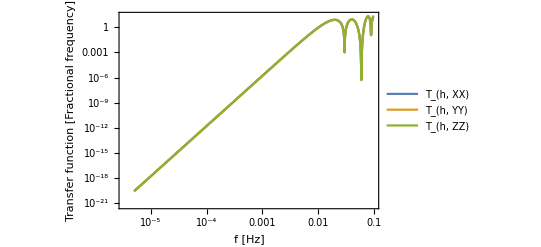

```mathematica
ListLogLogPlot[{Transpose[{freqs,Re[XX]}],Transpose[{freqs,Re[YY]}],Transpose[{freqs,Re[ZZ]}]},Joined->True,PlotLegends->Placed[{" T_(h, XX)"," T_(h, YY)"," T_(h, ZZ)"},{0.5,0.5}],Frame->True,FrameLabel->{"f [Hz]"," Transfer function [Fractional frequency]"},GridLines->Automatic,FrameTicks->Automatic]
```

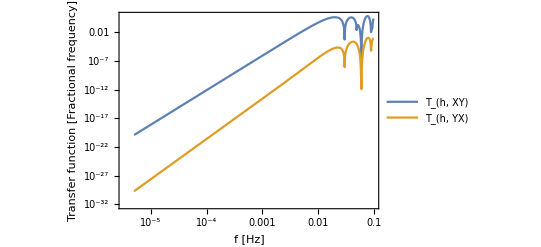

```mathematica
ListLogLogPlot[{Transpose[{freqs,Abs[Re[YX]]}],Transpose[{freqs,Abs[Im[YX]]}]},Joined->True,PlotLegends->Placed[{" T_(h, XY)"," T_(h, YX)"},{0.5,0.5}],Frame->True,FrameLabel->{"f [Hz]"," Transfer function [Fractional frequency]"},GridLines->Automatic,FrameTicks->Automatic]
```

```mathematica
XY=PSDXYZTable[[;;,1,2]];
YX=PSDXYZTable[[;;,2,1]];

XY == Conjugate[YX]
```

True

```mathematica
XZ=PSDXYZTable[[;;,1,3]];
```

```mathematica
YY=PSDXYZTable[[;;,2,2]];
```

```mathematica
ZZ=PSDXYZTable[[;;,3,3]];
```

```mathematica
Export["/Users/murmar/Documents/workspace/TDItransferfunction_martina_real.csv",Transpose[{freqs,AA,EE,TT}//SetPrecision[Re@#,$MachinePrecision]&//N]]
```

/Users/murmar/Documents/workspace/TDItransferfunction_martina2_real.csv

```mathematica
(*ζζ=PSDTable[[;;,3,3]];*)
```

```mathematica
AE=PSDTable[[;;,1,2]];
```

```mathematica
AT=PSDTable[[;;,1,3]];
```

```mathematica
ET=PSDTable[[;;,2,3]];
```

```mathematica
(*Aζ=PSDTable[[;;,1,3]];*)
```

```mathematica
(*Eζ=PSDTable[[;;,2,3]];
```

```mathematica
EElow=PSDTableeqlowf[[;;,2,2]];
```

```mathematica
ζζlow=PSDTablelowfreq[[;;,3,3]];
```

```mathematica
ζζVlow=PSDTablelowV2freq[[;;,3,3]];
```

```mathematica
ζζV2low=PSDTableVlowfreq2[[;;,3,3]];
```

```mathematica
ζζVlow2=PSDTableSLowζ1;
```

```mathematica
ζζVlow3=PSDTableVlowfreq[[;;,3,3]];
```

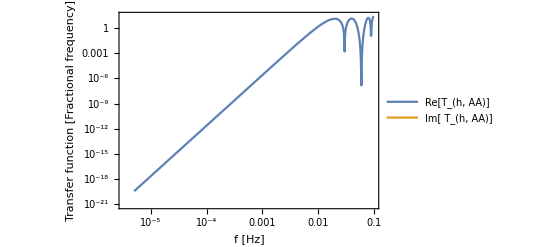

```mathematica
ListLogLogPlot[{Transpose[{freqs,Re[AA]}],Transpose[{freqs,Abs[Im[AA]]}]},Joined->True,PlotLegends->Placed[{" Re[T_(h, AA)]","Im[ T_(h, AA)]"},{0.5,0.5}],Frame->True,FrameLabel->{"f [Hz]"," Transfer function [Fractional frequency]"},GridLines->Automatic,FrameTicks->Automatic]
```

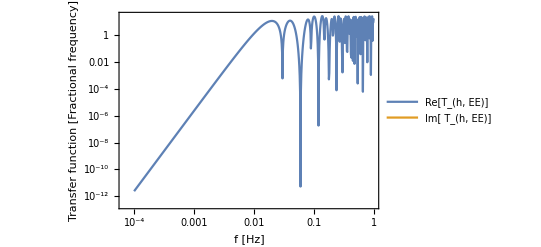

```mathematica
ListLogLogPlot[{Transpose[{freqs,Re[EE]}],Transpose[{freqs,Abs[Im[EE]]}]},Joined->True,PlotLegends->Placed[{" Re[T_(h, EE)]","Im[ T_(h, EE)]"},{0.5,0.5}],Frame->True,FrameLabel->{"f [Hz]"," Transfer function [Fractional frequency]"},GridLines->Automatic]
```

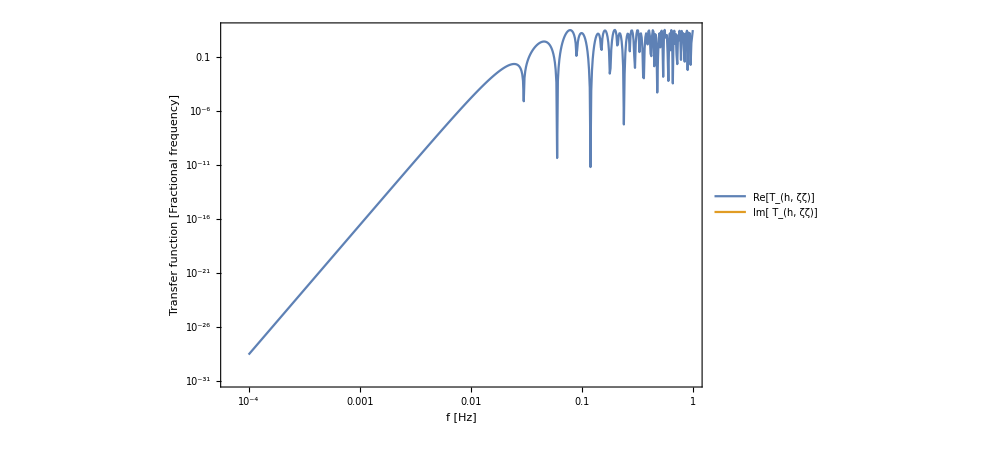

```mathematica
ListLogLogPlot[{Transpose[{freqs,Re[TT]}],Transpose[{freqs,Abs[Im[TT]]}]},Joined->True,PlotLegends->Placed[{" Re[T_(h, ζζ)]","Im[ T_(h, ζζ)]"},{0.5,0.5}],Frame->True,FrameLabel->{"f [Hz]"," Transfer function [Fractional frequency]"},GridLines->Automatic]
```

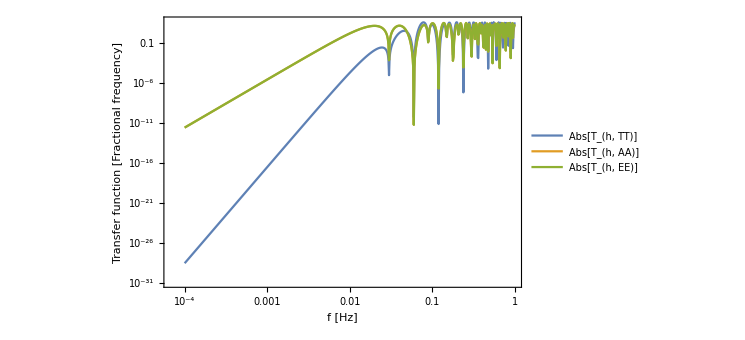

```mathematica
ListLogLogPlot[{Transpose[{freqs,Abs[TT]}],Transpose[{freqs,Abs[AA]}],Transpose[{freqs,Abs[EE]}]},Joined->True,PlotLegends->Placed[{" Abs[T_(h, TT)]","Abs[T_(h, AA)]","Abs[T_(h, EE)]"},{0.5,0.5}],Frame->True,FrameLabel->{"f [Hz]"," Transfer function [Fractional frequency]"},GridLines->Automatic]
```

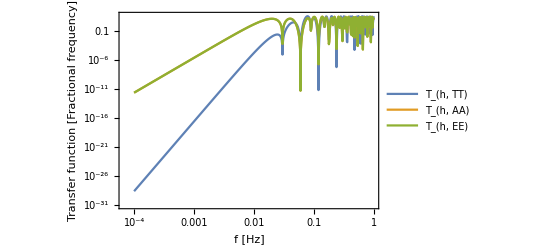

```mathematica
ListLogLogPlot[{Transpose[{freqs,Re[TT]}],Transpose[{freqs,Re[AA]}],Transpose[{freqs,Re[EE]}]},Joined->True,PlotLegends->Placed[{" Re[T_(h, TT)]","Re[T_(h, AA)]","Re[T_(h, EE)]"},{0.5,0.5}],Frame->True,FrameLabel->{"f [Hz]"," Transfer function [Fractional frequency]"},GridLines->Automatic]
```

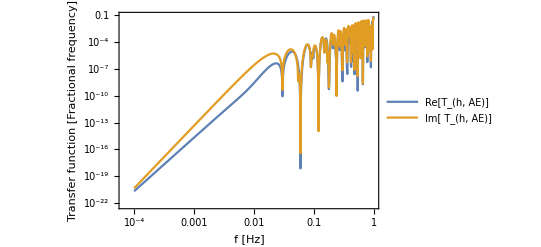

```mathematica
ListLogLogPlot[{Transpose[{freqs,Abs[Re[AE]]}],Transpose[{freqs,Abs[Im[AE]]}]},Joined->True,PlotLegends->Placed[{" Re[T_(h, AE)]","Im[ T_(h, AE)]"},{0.5,0.5}],Frame->True,FrameLabel->{"f [Hz]"," Transfer function [Fractional frequency]"},GridLines->Automatic]
```

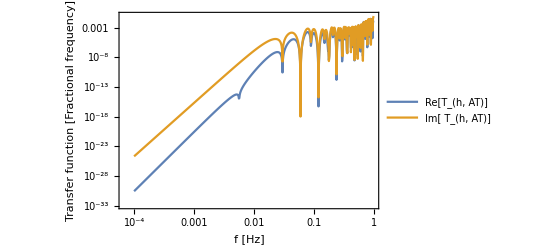

```mathematica
ListLogLogPlot[{Transpose[{freqs,Abs[Re[AT]]}],Transpose[{freqs,Abs[Im[AT]]}]},Joined->True,PlotLegends->Placed[{" Re[T_(h, AT)]","Im[ T_(h, AT)]"},{0.5,0.5}],Frame->True,FrameLabel->{"f [Hz]"," Transfer function [Fractional frequency]"},GridLines->Automatic]
```

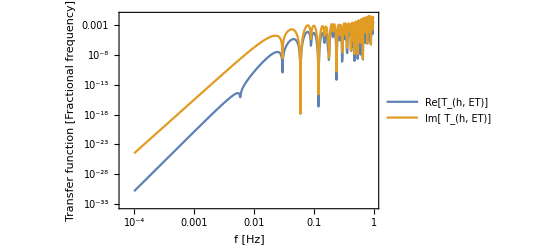

```mathematica
ListLogLogPlot[{Transpose[{freqs,Abs[Re[ET]]}],Transpose[{freqs,Abs[Im[ET]]}]},Joined->True,PlotLegends->Placed[{" Re[T_(h, ET)]","Im[ T_(h, ET)]"},{0.5,0.5}],Frame->True,FrameLabel->{"f [Hz]"," Transfer function [Fractional frequency]"},GridLines->Automatic]
```

```mathematica
UpsilonJon=(expr=Import["/Users/murmar/Downloads/Upsilon100000.csv","CSV"]//ToExpression;expr[[All,2]]);
```